```mathematica
(* Rearrange the positivity conditions for cubic polynomials to be in terms of assigned first and second derivative. *)
(*h=(U1-U0)/2;
v=X1-X0;
AA=(2h DX0)/v;
BB=(2h DX1)/v;
CC=(h^2 DDX0)/v;
DD=(h^2 DDX1)/v;*)
a=4(-DD);
b=6(DD-CC-2AA+5);
c=4(AA+CC);
d=AA;
(a+b+c+d)//ExpandAll//Simplify;
(b+2c+3d)//ExpandAll//Simplify;
(c+3d)//ExpandAll//Simplify;
(* Define usefully simplified version of constants. *)
alpha=30-7 AA+2( DD-CC);
beta=30-AA+2(CC+3DD);
gamma=7AA+4CC;
delta=AA;
Print[Simplify[ExpandAll[(a+b+c+d)]]===Simplify[ExpandAll[alpha]],"  ",
Simplify[ExpandAll[(b+2c+3d)]]===Simplify[ExpandAll[beta]],"  ",
Simplify[ExpandAll[(c+3d)]]===Simplify[ExpandAll[gamma]],"  ",
Simplify[ExpandAll[(d)]]===Simplify[ExpandAll[delta]]];
((beta-alpha)/2)^2//ExpandAll//Simplify
((gamma-delta)/2)^2//ExpandAll//Simplify
(alpha delta)//ExpandAll//Simplify
```

True  True  True  True

(3 AA+2 (CC+DD))^2

(3 AA+2 CC)^2

AA (30-7 AA-2 CC+2 DD)

```mathematica
(*;
   alpha ≥ 0;
   delta ≥ 0;
   ((beta-alpha)/-2)^2 ≤ alpha delta;
   ((gamma-delta)/-2)^2 ≤ alpha delta;
    (30-7AA)/2 ≤ a(CC - DD);
   (9 A^2 ≤ 30A - 7 A^2);
   (0 ≤ 30A - 16 A^2);
*)
(* If (B == 0);
  1. Make [α ≥ 0];
     A = min(A,3);
     a = max(1,(7(30/7-AA))/(2(CC-DD)));
     DDX0 = a DDX0;
     DDX1 = a DDX1;
  2. If (α > β) or (δ > γ);
       A = min(A, 15/8);
       C = ;
  3. ;
*)
```

```mathematica
Solve[30x-16 x^2==0]
```

{{x→0},{x→15/8}}

```mathematica
(* Figure out what changes to DX0, DX1, DDX0, and DDX1 are invariant to monotonicity. *)
v=X1-X0;
h=(U1-U0)/2;
A0=DX0*2*h/v;
B0=DX1*2*h/v;
C0=DDX0*h*(h/v);
D0=DDX1*h*(h/v);
a=B0;
b=4*(B0-D0);
c=30-6*(2*(A0+B0)+C0-D0);
d=4*(A0+C0);
e=A0;
alpha=b*a^(-3/4)*e^(-1/4);
beta=c*a^(-1/2)*e^(-1/2);
gamma=d*a^(-1/4)*e^(-3/4);
alpha=Collect[Simplify[ExpandAll[alpha]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
beta=Collect[Simplify[ExpandAll[beta]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
gamma=Collect[Simplify[Expand[gamma]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
Collect[alpha//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]//Together//Simplify
Collect[gamma//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]//Together//Simplify
Collect[beta//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]
Collect[-(beta+2)/2//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]
Collect[-2 √(beta-2)//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]
(* cDX0, cDX1, cDDX0, cDDX1 -> 1 *)
```

(A^(3/4) (4 DX1+DDX1 (U0-U1)))/(B^(3/4) DX0)

(B^(3/4) (4 DX0+DDX0 (-U0+U1)))/(A^(3/4) DX1)

(3 DX0 (-8 U0+8 U1))/(2 √A √B (X0-X1))+(3 DX1 (-8 U0+8 U1))/(2 √A √B (X0-X1))+(3 DDX1 (-U0^2+2 U0 U1-U1^2))/(2 √A √B (X0-X1))+(3 DDX0 (U0^2-2 U0 U1+U1^2))/(2 √A √B (X0-X1))+(3 (20 X0-20 X1))/(2 √A √B (X0-X1))

(6 DX0 (U0-U1))/(√A √B (X0-X1))+(6 DX1 (U0-U1))/(√A √B (X0-X1))+(DDX0 (-3 U0^2+6 U0 U1-3 U1^2))/(4 √A √B (X0-X1))+(DDX1 (3 U0^2-6 U0 U1+3 U1^2))/(4 √A √B (X0-X1))+(-60 X0-4 √A √B X0+60 X1+4 √A √B X1)/(4 √A √B (X0-X1))

-√2 √((-24 DX0 U0-24 DX1 U0+3 DDX0 U0^2-3 DDX1 U0^2+24 DX0 U1+24 DX1 U1-6 DDX0 U0 U1+6 DDX1 U0 U1+3 DDX0 U1^2-3 DDX1 U1^2+60 X0-4 √A √B X0-60 X1+4 √A √B X1)/(√A √B (X0-X1)))

```mathematica
(-3 U0^2+6 U0 U1-3 U1^2)//Simplify
(3 U0^2-6 U0 U1+3 U1^2)//Simplify
-60 X0-4 √A √B X0+60 X1+4 √A √B X1//Simplify
-24 DX0 U0-24 DX1 U0+3 DDX0 U0^2-3 DDX1 U0^2+24 DX0 U1+24 DX1 U1-6 DDX0 U0 U1+6 DDX1 U0 U1+3 DDX0 U1^2-3 DDX1 U1^2+60 X0-4 √A √B X0-60 X1+4 √A √B X1//Simplify
3(DDX0-DDX1)(U0-U1)^2-24 (DX0+DX1)(U0-U1)+(X0-X1)(60-4 √A √B)//ExpandAll//Simplify
```

-3 (U0-U1)^2

3 (U0-U1)^2

-4 (15+√A √B) (X0-X1)

3 DDX0 U0^2-3 DDX1 U0^2-24 DX0 (U0-U1)-24 DX1 (U0-U1)-6 DDX0 U0 U1+6 DDX1 U0 U1+3 DDX0 U1^2-3 DDX1 U1^2+60 X0-4 √A √B X0-60 X1+4 √A √B X1

3 DDX0 U0^2-3 DDX1 U0^2-24 DX0 (U0-U1)-24 DX1 (U0-U1)-6 DDX0 U0 U1+6 DDX1 U0 U1+3 DDX0 U1^2-3 DDX1 U1^2+60 X0-4 √A √B X0-60 X1+4 √A √B X1

-52 c (U0-U1)+3 DDX0 (U0-U1)^2-3 DDX1 (U0-U1)^2+60 (X0-X1)

```mathematica
(* When scaling DX0 and DX1 down at the same rate, identify how to keep beta constant. *)
ClearAll[U0,U1,X0,X1,DX0,DX1,DDX0,DDX1,A,B,v,h,c,d];
alpha=(4 B^(1/4))/A^(1/4)+(B^(1/4) DDX1 (U0-U1))/(A^(1/4) DX1);
gamma=(4 B^(3/4) DX0)/(A^(3/4) DX1)+(B^(3/4) DDX0 (U1-U0))/(A^(3/4) DX1);
beta=(3/2 (DDX0-DDX1) (U0-U1)^2+12 (DX0+DX1) (U1-U0)+30 (X0-X1))/(√A √B (X0-X1));
v=X1-X0;
h=(U1-U0)/2;
A=DX0*2*h/v;
B=DX1*2*h/v;
DX0=c;
DX1=c;
Collect[alpha//ExpandAll//Together//Simplify,{c,d}]
Collect[gamma//ExpandAll//Together//Simplify,{c,d}]
Collect[beta//ExpandAll//Together//Simplify,{c,d}]
(* When (DX0 = DX1 = c) we have: *)
alpha=(DDX1(U0-U1))/c+4;
gamma=4-(DDX0(U0-U1))/c;
beta=(3 (DDX0-DDX1) (U0-U1)^2+60 (X0-X1))/(2(U0-U1)c)-24;
(* Which implies for "alpha" to grow faster than "beta" we have: *)
DDX1(U0-U1)>(3 (DDX0-DDX1) (U0-U1)^2+60 (X0-X1))/(2(U0-U1));
DDX1>(3 (DDX0-DDX1) (U0-U1)^2+60 (X0-X1))/(2(U0-U1)^2);
2DDX1-3(DDX0-DDX1)>(60 (X0-X1))/(U0-U1)^2;
-(3DDX0+DDX1)>(60 (X0-X1))/(U0-U1)^2;
(3DDX0+DDX1)<(60(X1-X0))/(U1-U0)^2;
(* and similarly for "gamma" to grow faster than "beta" we have: *)
-DDX0(U0-U1)>(3 (DDX0-DDX1) (U0-U1)^2+60 (X0-X1))/(2(U0-U1));
-DDX0>(3 (DDX0-DDX1) (U0-U1)^2+60 (X0-X1))/(2(U0-U1)^2);
-2DDX0-3(DDX0-DDX1)>(60 (X0-X1))/(U0-U1)^2;
-(5DDX0+3DDX1)>(60 (X0-X1))/(U0-U1)^2;
(5DDX0+3DDX1)<(60 (X1-X0))/(U1-U0)^2;
```

4+(DDX1 U0-DDX1 U1)/c

4+(-DDX0 U0+DDX0 U1)/c

-24+(-3 DDX1 U0^2+3 DDX0 (U0-U1)^2+6 DDX1 U0 U1-3 DDX1 U1^2+60 X0-60 X1)/(2 c (U0-U1))

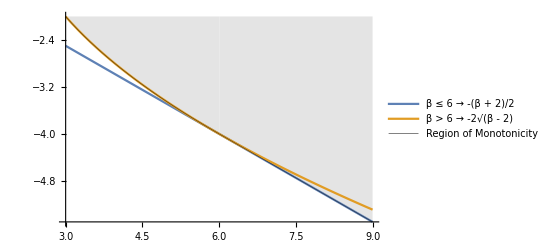

```mathematica
(* Plots of the lines representing conditions on β *)
Plot[{-(b+2)/2,-2 √(b-2),If[b≥6,-(b+2)/2,-2 √(b-2)]},{b,3,9},PlotLegends->{"β ≤ 6  →  -(β + 2)/2", "β > 6  →  -2√(β - 2)", "Region of Monotonicity"},Filling->{3->-2},FillingStyle->{3->LightGray},PlotStyle->{,,{Black,Thickness[.001],Opacity[.7]}}]
```

```mathematica
(* Construct a function for expanding out the monotonicity conditions to their final form (and algebraically simplifying). *)
isMonotone[DDX0_,DDX1_]:={
v=X1-X0;
h=(U1-U0)/2;
A0=DX0*2*h/v;
B0=DX1*2*h/v;
C0=DDX0*h*(h/v);
D0=DDX1*h*(h/v);
a=B0;
b=4*(B0-D0);
c=30-6*(2*(A0+B0)+C0-D0);
d=4*(A0+C0);
e=A0;
alpha=b*a^(-3/4)*e^(-1/4);
beta=c*a^(-1/2)*e^(-1/2);
gamma=d*a^(-1/4)*e^(-3/4);
alpha=Collect[Simplify[ExpandAll[alpha]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
beta=Collect[Simplify[ExpandAll[beta]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
gamma=Collect[Simplify[Expand[gamma]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
Print["α: ",alpha];
Print["β: ",beta];
Print["γ: ",gamma];
}[[1]];
isMonotone[DDX0,DDX1];
(*Print["\n-------------------------------------\n"]
Solve[alpha==(-(beta+2)/2)==gamma,{DDX0,DDX1}]*)
(*Print["\n-------------------------------------\n"]
Solve[alpha==(-2 √(beta-2))==gamma,{DDX0,DDX1}]*)
```

α: (4 A^(3/4) DX1)/(B^(3/4) DX0)+(A^(3/4) DDX1 (U0-U1))/(B^(3/4) DX0)

β: (3 DDX1 (-U0^2+2 U0 U1-U1^2))/(2 √A √B (X0-X1))+(3 DDX0 (U0^2-2 U0 U1+U1^2))/(2 √A √B (X0-X1))+(3 (-8 DX0 U0-8 DX1 U0+8 DX0 U1+8 DX1 U1+20 X0-20 X1))/(2 √A √B (X0-X1))

γ: (4 B^(3/4) DX0)/(A^(3/4) DX1)+(B^(3/4) DDX0 (-U0+U1))/(A^(3/4) DX1)

```mathematica
(* Print the true and simplified expressions to verify that they are identical. *)
ClearAll[U0,U1,X0,X1,DX0,DX1,DDX0,DDX1,A,B,A0,B0]
A0=DX0*(U0-U1)/(X0-X1);
B0=DX1*(U0-U1)/(X0-X1);

aFunc[DDX1_]:=DDX1*((U0-U1)*B0^(1/4))/(DX1*A0^(1/4))+(4*B0^(1/4))/A0^(1/4);
gFunc[DDX0_]:=DDX0*((U1-U0)*B0^(3/4))/(DX1*A0^(3/4))+(4*DX0*B0^(3/4))/(DX1*A0^(3/4));
bFunc[DDX0_,DDX1_]:=(DDX0-DDX1)*(3*(U0-U1)^2)/(2*(X0-X1)*A0^(1/2)*B0^(1/2))+(12*(DX0+DX1)*(U1-U0)+30*(X0-X1))/((X0-X1)*A0^(1/2)*B0^(1/2));
Print["α: ",aFunc[DDX1]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B}];
Print["β: ",bFunc[DDX0,DDX1]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B}];
Print["γ: ",gFunc[DDX0]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B}];
Print["-----------------------------------------------------------------------------"]
Print["α: ",Collect[Simplify[ExpandAll[aFunc[DDX1]]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B}];
Print["β: ",Collect[Simplify[ExpandAll[bFunc[DDX0,DDX1]]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B}];
Print["γ: ",Collect[Simplify[ExpandAll[gFunc[DDX0]]],{DDX0,DDX1}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B}];
```

α: (4 B^(1/4))/A^(1/4)+(B^(1/4) DDX1 (U0-U1))/(A^(1/4) DX1)

β: (3 (DDX0-DDX1) (U0-U1)^2)/(2 √A √B (X0-X1))+(12 (DX0+DX1) (-U0+U1)+30 (X0-X1))/(√A √B (X0-X1))

γ: (4 B^(3/4) DX0)/(A^(3/4) DX1)+(B^(3/4) DDX0 (-U0+U1))/(A^(3/4) DX1)

-----------------------------------------------------------------------------

α: (4 B^(1/4))/A^(1/4)+(B^(1/4) DDX1 (U0-U1))/(A^(1/4) DX1)

β: (3 DDX1 (-U0^2+2 U0 U1-U1^2))/(2 √A √B (X0-X1))+(3 DDX0 (U0^2-2 U0 U1+U1^2))/(2 √A √B (X0-X1))+(3 (-8 DX0 U0-8 DX1 U0+8 DX0 U1+8 DX1 U1+20 X0-20 X1))/(2 √A √B (X0-X1))

γ: (4 B^(3/4) DX0)/(A^(3/4) DX1)+(B^(3/4) DDX0 (-U0+U1))/(A^(3/4) DX1)

```mathematica
(* Computation of Subscript[τ, 1] *)
tau1[A_,B_]:=24+2 √(A B)-3(A+B);
tau1[ρ A,ρ B]
Solve[tau1[ρ A,ρ B]==0,ρ]
```

24+2 √(A B ρ^2)-3 (A ρ+B ρ)

{{ρ→(24 (3 A-2 √A √B+3 B))/(9 A^2+14 A B+9 B^2)},{ρ→(24 (3 A+2 √A √B+3 B))/(9 A^2+14 A B+9 B^2)}}

-120/23+1728/(23 x)+1152/(23 √(x^2))

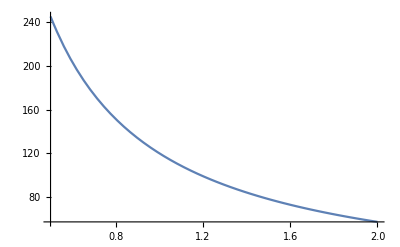

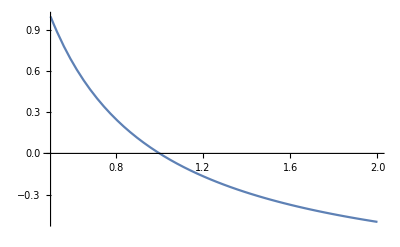

```mathematica
(* Plot the τ function to see why the algebraic solution works. *)
constant[ab_]:=24(3(ab)+2(ab^2)^(1/2))/(9*(ab^2)+14*(ab^2))
tau[ab_]:=24+2(ab^2)^(1/2)-3ab
tau[x]constant[x]//Simplify//Expand
Plot[constant[x]tau[x],{x,.5,2}]
Plot[1/x-1,{x,.5,2}]
```

## Failed Experiments

```mathematica
(* Expand out the cubic scenario to see if there are simplifications in terms of DX0, DX1, DDX0, DDX1   (FAILED)   *)
Print["alpha: ",Collect[alpha//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]];
Print["beta:  ",Collect[beta//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]];
Print["gamma: ",Collect[gamma//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]];
Print["delta: ",Collect[delta//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]];
alpha=30+(((DDX0-DDX1) (U0-U1)-2(7DX0+8DX1)) (U0-U1))/(2 (X0-X1));
beta=30-(((DDX0+3DDX1) (U0-U1)+2(DX0+12DX1)) (U0-U1))/(2 (X0-X1));
gamma=((7 DX0-DDX0(U0-U1))(U0-U1))/(X0-X1);
delta=(DX0(U0-U1))/(X0-X1);
Collect[alpha//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]
Collect[beta//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]
Collect[gamma//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]
Collect[delta//ExpandAll//Simplify,{DX0,DX1,DDX0,DDX1}]

bmas=((6 DX0-4 DX1-(DDX0+DDX1) (U0-U1))^2 (U0-U1)^2)/(2^2(X0-X1)^2);
gmds=((6 DX0-DDX0 (U0-U1))^2(U0-U1)^2)/(2^2(X0-X1)^2);
ad=(DX0(U0-U1)((DDX0-DDX1) (U0-U1)^2-2(7 DX0+8DX1) (U0-U1)+60(X0-X1)))/(2(X0-X1)^2);
Print[Simplify[ExpandAll[bmas]]===Simplify[ExpandAll[((beta-alpha)/-2)^2]],"  ",
Simplify[ExpandAll[gmds]]===Simplify[ExpandAll[((gamma-delta)/-2)^2]],"  ",
Simplify[ExpandAll[ad]]===Simplify[ExpandAll[alpha delta]]];
bmas-ad//ExpandAll//Simplify;
gmds-ad//ExpandAll//Simplify;
```

```mathematica
(* Explicitly define the monotonicity conditions, look for simple solution expression. (FAILED) *)
v=X1-X0;
h=(U1-U0)/2;
A0=DX0*2*h/v;
B0=DX1*2*h/v;
C0=DDX0*h*(h/v);
D0=DDX1*h*(h/v);
a=B0;
b=4*(B0-D0);
c=30-6*(2*(A0+B0)+C0-D0);
d=4*(A0+C0);
e=A0;
alpha=b*a^(-3/4)*e^(-1/4);
beta=c*a^(-1/2)*e^(-1/2);
gamma=d*a^(-1/4)*e^(-3/4);
alpha=Collect[Simplify[Expand[alpha]],{DDX0,DDX1}];
beta=Collect[Simplify[Expand[beta]],{DDX0,DDX1}];
gamma=Collect[Simplify[Expand[gamma]],{DDX0,DDX1}];
(* Check to see what will happen to the monotonicity inequality as DX0 and DX1 are decreased (towards 0). *)
(*
U0=0;
U1=1;
X0=0;
X1=1;
DDX0=1;
DDX1=1;
DX0=DX1;
*)
(alpha-(-(beta+2)/2))//Expand
(alpha-(-2 √(beta-2)))//Expand
```

```mathematica
(* Computations for solving that appropriate α and γ to satisfy the conditions with β. (FAILED) *)
v=X1-X0;
tDDX0=-(√A0)/4(7 √A0+3 √B0);
tDDX1=(√B0)/4(3 √A0+7 √B0);
fDDX0=(ratio)DDX0+(1-ratio)tDDX0;
fDDX1=(ratio)DDX1+(1-ratio)tDDX1;
h=(U1-U0)/2;
A0=DX0*2*h/v;
B0=DX1*2*h/v;
C0=fDDX0*h*(h/v);
D0=fDDX1*h*(h/v);
a=B0;
b=4*(B0-D0);
c=30-6*(2*(A0+B0)+C0-D0);
d=4*(A0+C0);
e=A0;
alpha=b*a^(-3/4)*e^(-1/4);
beta=c*a^(-1/2)*e^(-1/2);
gamma=d*a^(-1/4)*e^(-3/4);
(* Simplify the expressions. Replace[<expression>,{(DX0 (U0-U1))/(X0-X1)->A0,(DX1 (U0-U1))/(X0-X1)->B0}] *)
alpha=Collect[Simplify[ExpandAll[alpha]],{ratio}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
gamma=Collect[Simplify[ExpandAll[gamma]],{ratio}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
beta=Collect[Simplify[ExpandAll[beta]],{ratio}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
Print[]
Print["alpha = ",alpha]
Print["gamma = ",gamma]
Print["beta  = ",beta]
(* Get the coefficient lists in terms of ratio, rewrite in simple form. *)
acl=CoefficientList[alpha,ratio];
gcl=CoefficientList[gamma,ratio];
bcl=CoefficientList[beta,ratio];
Clear[ax,ay,gx,gy,bx,by];
alpha=ax(ratio)+ay;
gamma=gx(ratio)+gy;
beta=bx(ratio)+by;
Print[]
Print["----------------------------------------------------------------"]
Print[]
(* Compute all of the solutions to the problem. *)
(* CASE 1: (alpha == bound) AND (bound ≤ 6) *)
solution=Solve[{alpha==(-(beta+2)/2)},{ratio}];
sol1=solution[[1]][[1]][[2]];
(* CASE 2: (gamma == bound) AND (bound ≤ 6) *)
solution=Solve[{gamma==(-(beta+2)/2)},{ratio}];
sol2=solution[[1]][[1]][[2]];
(* CASE 3: (alpha == bound) AND (bound > 6) *)
solution=Solve[{alpha==(-2 √(beta-2))},{ratio}];
sol3a=solution[[1]][[1]][[2]];
sol3b=solution[[2]][[1]][[2]];
(* CASE 4: (gamma == bound) AND (bound > 6) *)
solution=Solve[{gamma==(-2 √(beta-2))},{ratio}];
sol4a=solution[[1]][[1]][[2]];
sol4b=solution[[2]][[1]][[2]];
(* ----------------------------------------------------------------------------- *)
ax=acl[[1]];
ay=acl[[2]];
gx=gcl[[1]];
gy=gcl[[2]];
bx=bcl[[1]];
by=bcl[[2]];
(* Print all of the solutions out in a readable form (that can be copied to code). *)
Print["Alpha equals bound for beta <= 6"]
Print["ratio = ",sol1//ExpandAll//Simplify//FortranForm]
Print[]

Print["Gamma equals bound for beta <= 6"]
Print["ratio = ",sol2//ExpandAll//Simplify//FortranForm]
Print[]


Print["Alpha equals bound for beta > 6"]
Print["ratio = ",sol3a//Simplify//FortranForm]
Print["ratio = ",sol3b//Simplify//FortranForm]
Print[]

Print["Gamma equals bound for beta > 6"]
Print["ratio = ",sol4a//Simplify//FortranForm]
Print["ratio = ",sol4b//Simplify//FortranForm]
Print[]

(* Verify each of the above solutions algebraically. *)
ratio=sol1;
lhs=Simplify[ExpandAll[alpha]];
rhs=Simplify[ExpandAll[(-(beta+2)/2)]];
Print["Case 1 works: ",lhs===rhs]

ratio=sol2;
lhs=Simplify[ExpandAll[gamma]];
rhs=Simplify[ExpandAll[(-(beta+2)/2)]];
Print["Case 2 works: ",lhs===rhs]

(*ratio=sol3a;
lhs=Simplify[ExpandAll[alpha]];
rhs=Simplify[ExpandAll[(-2 √(beta-2))]];
Print["Case 3a works: ",lhs===rhs]
ratio=sol3b;
lhs=Simplify[ExpandAll[alpha]];
rhs=Simplify[ExpandAll[(-2 √(beta-2))]];
Print["Case 3b works: ",lhs===rhs]

ratio=sol4a;
lhs=Simplify[ExpandAll[gamma]];
rhs=Simplify[ExpandAll[(-2 √(beta-2))]];
Print["Case 4a works: ",lhs===rhs]
ratio=sol4b;
lhs=Simplify[ExpandAll[gamma]];
rhs=Simplify[ExpandAll[(-2 √(beta-2))]];
Print["Case 4b works: ",lhs===rhs]*)
```